```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>=0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals&&a∈Reals&&a>0&&lam∈Reals&&lam>0;
```

system parameter:
A (int) : total number of particles
F (int) : number of fragments
Z (int array) : number of particles in fragments
d (int) : number of spatial dimensions (ECCE: do not use; from the 1-dim result, one should be able to deduce the d-dim variant)

```mathematica
spacedim=3;
A=5;
F=3;
Z={2,2,1};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
(* (AB)-(AB)-(A) *)
idPart={{1,3,5},{2,4}};
idPairs={};
Do[AppendTo[idPairs,DeleteDuplicates[Sort[#,Less]&/@Select[Tuples[idPartp,2],#[[1]]≠#[[2]]&]]],{idPartp,idPart}]
idPairs=Flatten[idPairs,1];Print["Identical-particle indices: ",idPairs];
```

Identical-particle indices: {{1,3},{1,5},{3,5},{2,4}}

```mathematica
tmp=Range[#]&@Accumulate[Z];Znbr={tmp[[1]]};
Do[AppendTo[Znbr,Complement[tmp[[nfrg+1]],tmp[[nfrg]]]],{nfrg,Length[tmp]-1}]
frgcomb2=Select[Tuples[Range[Length[Z]],2],#[[1]]≠#[[2]]&&#[[1]]<#[[2]]&];
intPairs={};
Do[AppendTo[intPairs,Tuples[{Znbr[[frgcomb2[[n]][[1]]]],Znbr[[frgcomb2[[n]][[2]]]]}]],{n,Range[Length[frgcomb2]]}];
intPairs=Flatten[intPairs,1];
intBosePairs=Complement[intPairs,idPairs];

frgcomb3=DeleteDuplicates[Sort[#,Less]&/@Tuples[Range[Length[Z]],3]];
intTriples={};
Do[AppendTo[intTriples,Tuples[{Znbr[[frgcomb3[[n]][[1]]]],Znbr[[frgcomb3[[n]][[2]]]],Znbr[[frgcomb3[[n]][[3]]]]}]],{n,Range[Length[frgcomb3]]}]
intTriples=DeleteDuplicates[Sort[#,Less]&/@Select[Flatten[intTriples,1],DuplicateFreeQ[#]&]];
intBoseTriples=intTriples;
Do[intBoseTriples=Select[intBoseTriples,Length[Complement[#,idPairsp]]≠1&],{idPairsp,idPairs}];

Print["∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = "<>ToString[Length[intBosePairs]]<>"·δ_ij + "<>ToString[Length[intBoseTriples]]<>"·δ_ijδ_ik"]
Print["Pairs = ",intBosePairs,"   Triples = ",intBoseTriples]
intPart=Join[Table[AppendTo[intBosePairs[[n]],intBosePairs[[n]][[1]]],{n,Length[intBosePairs]}],intBoseTriples,{{1,1,1}}];
```

∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = 4·δ_ij + 0·δ_ijδ_ik

Pairs = {{1,4},{2,3},{2,5},{4,5}}   Triples = {}

coordinate transformations:
single-particle   →  cluster-relative : T^-1
cluster-relative  →  single-particle  : r_single=T·r_cluster

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
Do[
col=ConstantArray[0,A];
Do[
(col[[#]]=1/Total[(Length[#]&/@Znbr[[;;njac]])])&/@Znbr[[nR]];
,{nR,Range[njac]}];
(col[[#]]=-1/Length[Znbr[[njac+1]]])&/@Znbr[[njac+1]];
AppendTo[SingleToCluster,col]
,{njac,Range[F-1]}]

AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
Svec=Array[If[A-F<##<A,-I Subscript[s, ##-(A-F)],0]&,{A}]
Svars=Array[Subscript[s, ##]&,{F-1}];
ParCoordVec=Array[If[A-F<##<A,Subscript[Rp, ##-(A-F)],0]&,{A}]

AppendTo[Cluster,#]&/@ArrayFlatten[Array[Subscript[R, ##]&,{F-1}],1];AppendTo[Cluster,"(R⃗)_cm"];
Tmatinv=SingleToCluster;
Tmat=Inverse[SingleToCluster];

TmatinvRel=Table[If[(A-F<m<A),Tmatinv[[m,n]],0],{m,A},{n,A}];

Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Single//MatrixForm,"=",Tmat//MatrixForm,"·",Cluster//MatrixForm]
Print[Cluster//MatrixForm,"=",TmatinvRel//MatrixForm,"·",Single//MatrixForm]
```

{0,0,-ⅈ s_1,-ⅈ s_2,0}

{0,0,Rp_1,Rp_2,0}

((r̄)_1
(r̄)_3
R_1
R_2
(R⃗)_cm)=(1/2 | -1/2 | 0 | 0 | 0
0 | 0 | 1/2 | -1/2 | 0
1/2 | 1/2 | -1/2 | -1/2 | 0
1/4 | 1/4 | 1/4 | 1/4 | -1
1/5 | 1/5 | 1/5 | 1/5 | 1/5)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4
(r⃗)_5)

((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4
(r⃗)_5)=(1 | 0 | 1/2 | 1/5 | 1
-1 | 0 | 1/2 | 1/5 | 1
0 | 1 | -1/2 | 1/5 | 1
0 | -1 | -1/2 | 1/5 | 1
0 | 0 | 0 | -4/5 | 1)·((r̄)_1
(r̄)_3
R_1
R_2
(R⃗)_cm)

((r̄)_1
(r̄)_3
R_1
R_2
(R⃗)_cm)=(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1/2 | 1/2 | -1/2 | -1/2 | 0
1/4 | 1/4 | 1/4 | 1/4 | -1
0 | 0 | 0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4
(r⃗)_5)

quadratic form of fragment wave functions in cluster-relative coordinates:
ϕ_A ϕ_B=e^(-α_1/2(2 ∑_(j=1)^(A_1-1) r_j^2+∑_(j≠k)^(A_1-1) r_j r_k))·e^(1↔2)=∏_(i∈{1,2}) e^(-1/2(r_1,…,r_(A_i-1))(2 α_i
α_i
α_iα_i
2 α_i
α_iα_i
α_i
2 α_i) (r_1
⋮
r_(A_i-1)))
the matrix is set up row-wise
in the i-th row, the quadratic form of the j-th fragment is placed
with i-1 being the number of fragments with n<j which contain more than a single particle

```mathematica
Wmat=Table[0,{m,1,A},{n,1,A}];
Do[(If[#[[1]]==#[[2]],Wmat[[Znbr[zn][[-1]]-1+#[[1]]]][[Znbr[zn][[-1]]-1+#[[2]]]]=2 Subscript[a, zn],Wmat[[Znbr[zn][[-1]]-1+#[[1]]]][[Znbr[zn][[-1]]-1+#[[2]]]]=Subscript[a, zn]])&/@(Tuples[Range[Z[[zn]]-1],2]),{zn,1,Length[Z]}];
Print[Wmat//MatrixForm]
```

(2 a_1 | 0 | 0 | 0 | 0
0 | 2 a_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

matrix representation of the permutation (single-particle coordinates):
i)  list of all permutations = product of permutations amongst sets of identical particles, e.g., S_3⊗S_2 for an AB-AB-A symmetry
ii) represent each permutation by a matrix with a single unit entry per row *and* column

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];

interFragmentAntisymmetrizer=Permute[Flatten[#],Flatten[idPart]]&/@Tuples[Flatten[Permutations[#]&/@idPart,0]];

permMats={};
Do[
ptmp=ConstantArray[0,{A,A}];
Do[ptmp[[row,perm[[row]]]]=1,{row,A}];
AppendTo[permMats,{Signature[perm],ptmp}];
,{perm,interFragmentAntisymmetrizer}];

Print["(Â)_AB = ",NumberForm[Signature[#],NumberSigns->{"-", "+"}]," ",#]&/@interFragmentAntisymmetrizer;
Print["|(Â)_AB| = ",Length[DeleteDuplicates[interFragmentAntisymmetrizer]]];
```

(Â)_AB = +1 {1,2,3,4,5}

(Â)_AB = -1 {1,4,3,2,5}

(Â)_AB = -1 {1,2,5,4,3}

(Â)_AB = +1 {1,4,5,2,3}

(Â)_AB = -1 {3,2,1,4,5}

(Â)_AB = +1 {3,4,1,2,5}

(Â)_AB = +1 {3,2,5,4,1}

(Â)_AB = -1 {3,4,5,2,1}

(Â)_AB = +1 {5,2,1,4,3}

(Â)_AB = -1 {5,4,1,2,3}

(Â)_AB = -1 {5,2,3,4,1}

(Â)_AB = +1 {5,4,3,2,1}

|(Â)_AB| = 12

quadratic form of a two-body Gaussian interaction in cluster-relative coordinates:
V_(F_1 F_2)=∑_((i∈F_1)_(j∈F_2)) e^(-(λ(r_i-r_j))^2)

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_,λ_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==j)),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_,λ_]:=Transpose[Pv[i,j].Tmat].Vr[i,j,λ].Pv[i,j].Tmat;
Vijk[i_,j_,k_,λ_]:=Transpose[Pv[i,j].Tmat].Vr[i,j,λ].Pv[i,j].Tmat+Transpose[Pv[i,k].Tmat].Vr[i,k,λ].Pv[i,k].Tmat;
```

full quadratic form of a two-body Gaussian interaction between i,j and a permutation of particles m,n (matrix representation in cluster-relative coordinates):
dimer-dimer w/o discrete scale invariance:  V=δ_13+δ_23+δ_24+δ_234+δ_123    A=OverHat[1]-P_14

Integration:

∫d^3(ρ_(1…F-1)^,,s_(1…F-1),r_(cluster-internal))
i)  cluster-coord
ii) Fourier backtransformation of δ_(ρ-ρ^,)=(2π)^-n∫d^(n)s e^(-is(ρ-ρ^,))

```mathematica
{ivtest,jvtest,kvtest}=intPart[[-2]]
testperm=2;(* 1 = Identity *)
testl="λ";

Wfull[iv_,jv_,kv_,permu_,λ_]:=Simplify[Wmat+Vijk[iv,jv,kv,λ]+Transpose[(Tmatinv.permMats[[permu]][[2]].Tmat)].Wmat.(Tmatinv.permMats[[permu]][[2]].Tmat)];
Sfull[permu_]:=Simplify[(Transpose[TmatinvRel.permMats[[permu]][[2]].Tmat].Svec)];
Amat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[1;;(A-F),1;;(A-F)]];

(* 3-fragment structure hard coded *)
Bvec[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[;;A-F,A-F+1;;A-1]].Cluster[[A-F+1;;A-1]];

Dvec[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[;;A-F,A]] Cluster[[A]];
Evec[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-F+1;;A-1,A]] Cluster[[A]];
Ffac[iv_,jv_,kv_,permu_,λ_]:=Simplify[Cluster[[A]] Wfull[iv,jv,kv,permu,λ][[A,A]] Cluster[[A]]];

InhomoVec[iv_,jv_,kv_,permu_,λ_]:=-Bvec[iv,jv,kv,permu,λ]+Sfull[permu][[;;A-F]]

Cmat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-F+1;;A-1,A-F+1;;A-1]];


Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"   is symmetric? ",SymmetricMatrixQ[Wfull[ivtest,jvtest,kvtest,testperm,testl]],"      (S̲)_full = s⃗·(T_ρ^-1PT) = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest,testl]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest,testl]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm,testl]]]//MatrixForm,"         B⃗ = ",Bvec[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"           C̲ = ",Cmat[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"           D̲ = ",Dvec[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"           E̲ = ",Evec[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"           F = ",Ffac[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm]
Print["      Inhomo = s⃗·(T_ρ^-1PT)-B·ρ⃗ = ",InhomoVec[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm]
```

{4,5,4}

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (1/2 (5 a_1+a_2) | 1/2 (a_1+a_2) | 1/2 (a_1-a_2) | 0 | 0
1/2 (a_1+a_2) | 1/2 (4 λ+a_1+5 a_2) | 1/2 (2 λ+a_1-a_2) | -2 λ | 0
1/2 (a_1-a_2) | 1/2 (2 λ+a_1-a_2) | 1/2 (λ+a_1+a_2) | -λ | 0
0 | -2 λ | -λ | 2 λ | 0
0 | 0 | 0 | 0 | 0)   is symmetric? True      (S̲)_full = s⃗·(T_ρ^-1PT) = (-ⅈ s_1
ⅈ s_1
0
-ⅈ s_2
0)         (V̲)_ij = (0 | 0 | 0 | 0 | 0
0 | 2 λ | λ | -2 λ | 0
0 | λ | λ/2 | -λ | 0
0 | -2 λ | -λ | 2 λ | 0
0 | 0 | 0 | 0 | 0)         (V̲)_ijk = (0 | 0 | 0 | 0 | 0
0 | 2 λ | λ | -2 λ | 0
0 | λ | λ/2 | -λ | 0
0 | -2 λ | -λ | 2 λ | 0
0 | 0 | 0 | 0 | 0)

A̲ = (1/2 (5 a_1+a_2) | 1/2 (a_1+a_2)
1/2 (a_1+a_2) | 1/2 (4 λ+a_1+5 a_2))         (A̲)^-1 = ((4 λ+a_1+5 a_2)/(2 (a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2))) | -(a_1+a_2)/(2 (a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2)))
-(a_1+a_2)/(2 (a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2))) | (5 a_1+a_2)/(2 (a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2))))         B⃗ = (1/2 (a_1-a_2) R_1
1/2 (2 λ+a_1-a_2) R_1-2 λ R_2)           C̲ = (1/2 (λ+a_1+a_2) | -λ
-λ | 2 λ)           D̲ = (0
0)           E̲ = (0
0)           F = 0

Inhomo = s⃗·(T_ρ^-1PT)-B·ρ⃗ = (-1/2 (a_1-a_2) R_1-ⅈ s_1
-1/2 (2 λ+a_1-a_2) R_1+2 λ R_2+ⅈ s_1)

```mathematica
ECCE: hard-wired 3-fragment structure
```

```mathematica
scoeff[iv_,jv_,kv_,permu_,λ_]:=Simplify[1/2 InhomoVec[iv,jv,kv,permu,λ].Inverse[Amat[iv,jv,kv,permu,λ]].InhomoVec[iv,jv,kv,permu,λ]-1/2 Cluster[[A-F+1;;A-1]].Cmat[iv,jv,kv,permu,λ].Cluster[[A-F+1;;A-1]]+Sfull[permu][[A-F+1;;A-1]].Cluster[[A-F+1;;A-1]]-Svec.ParCoordVec];

Kmat[iv_,jv_,kv_,permu_,λ_]:=Block[{SvecCoffMat},

SvecCoffMat=PadRight[CoefficientList[scoeff[iv,jv,kv,permu,λ],Svars],{3,3}];

Simplify[-2 (DiagonalMatrix[{SvecCoffMat[[3,1]],SvecCoffMat[[1,3]]}]+1/2 Reverse[DiagonalMatrix[{SvecCoffMat[[2,2]],SvecCoffMat[[2,2]]}]])]
];


S5[iv_,jv_,kv_,permu_,λ_]:=Block[{SvecCoffMat},
SvecCoffMat=PadRight[CoefficientList[scoeff[iv,jv,kv,permu,λ],Svars],{3,3}];
{Simplify[SvecCoffMat[[2,1]]],Simplify[SvecCoffMat[[1,2]]]}
];

S6[iv_,jv_,kv_,permu_,λ_]:=Block[{SvecCoffMat},
SvecCoffMat=PadRight[CoefficientList[scoeff[iv,jv,kv,permu,λ],Svars],{3,3}];
Simplify[SvecCoffMat[[1,1]]]
];

Kmatinv[iv_,jv_,kv_,permu_,λ_]:=Block[{Kmatr},
Kmatr=Kmat[iv,jv,kv,permu,λ];
(*dia={};
Do[If[ToString[ent]=="0",AppendTo[dia,0],AppendTo[dia,1/ent]],{ent,Diagonal[Kmatr]}];
dia*)
If[MatrixRank[Kmatr]≠3,kinv=DiagonalMatrix[Table[If[ToString[diage]≠"0",1/diage,0],{diage,Diagonal[Kmatr]}]],kinv=Inverse[Kmatr]];
kinv
];

Print[S6[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm," + ",S5[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"s⃗  +s⃗·",Kmat[ivtest,jvtest,kvtest,testperm,testl]//MatrixForm,"·s⃗"]
```

-(λ a_2^2 (R_1-2 R_2)^2+a_1^2 ((λ+8 a_2) R_1^2+4 λ R_1 R_2+4 λ R_2^2)+2 a_1 a_2 ((9 λ+4 a_2) R_1^2-16 λ R_1 R_2+12 λ R_2^2))/(4 (a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2))) + (-(ⅈ (a_1^2 (R_1-Rp_1)+a_2 ((2 λ+a_2) R_1-2 λ R_2-(λ+a_2) Rp_1)+a_1 (2 (λ-a_2) R_1-6 λ R_2-(5 λ+6 a_2) Rp_1)))/(a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2))
-ⅈ (R_2-Rp_2))s⃗  +s⃗·((2 (λ+2 a_1+2 a_2))/(a_1^2+a_2 (λ+a_2)+a_1 (5 λ+6 a_2)) | 0
0 | 0)·s⃗

```mathematica
expo=Simplify[1/2 S5[ivtest,jvtest,kvtest,testperm,testl].Kmatinv[ivtest,jvtest,kvtest,testperm,testl].S5[ivtest,jvtest,kvtest,testperm,testl]+S6[ivtest,jvtest,kvtest,testperm,testl]]
CoefficientList[expo,Cluster[[A-F+1;;A-1]]]//MatrixForm
CoefficientList[expo,ParCoordVec[[A-F+1;;A-1]]]//MatrixForm
```

-(2 λ R_1^2 α_1 α_2)/(λ α_2+α_1 (λ+2 α_2))

(0
0
-(2 λ α_1 α_2)/(λ α_2+α_1 (λ+2 α_2)))

(-(2 λ R_1^2 α_1 α_2)/(λ α_2+α_1 (λ+2 α_2)))

s - integration

(T̂-E)_direct                                                                            :  λ=0  ,  i_p=j_p                  ⇒P̂=𝟙
δ_13^X (no scale invariance (ab)-(ca) dimer-dimer)  :  λ=Λ ,  i_p=1 ,j_p=4 ⇒(P̂)_14
ECCE:  ∫d^(spacedim)(r_1,…,r_(A-2),s)ϕ_A ϕ_B δ(s)=(2π)^(spacedim/2)/((2π)^spacedim(√(det(K)))^spacedim)((2π)^(dim(W)/2)/(√(det(W_((A-2)×(A-2))))))^spacedim

```mathematica
genericRGMEQcomponent[a1_,a2_,lec_,lam_,ii_,jj_,kk_,permu_]:=Module[{λ,parcov},

parcov=ParCoordVec[[A-F+1;;A-1]];

coffli=CoefficientList[
1/2 S5[ii,jj,kk,permu,lam].Kmatinv[ii,jj,kk,permu,lam].S5[ii,jj,kk,permu,lam]+S6[ii,jj,kk,permu,lam]
,parcov];
Rcoeff=PadRight[coffli,{3,3}];

rp1sq=Simplify[Rcoeff[[3,1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
rp2sq=Simplify[Rcoeff[[1,3]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
rp1=Simplify[Rcoeff[[2,1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
rp2=Simplify[Rcoeff[[1,2]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
rp1rp2=Simplify[Rcoeff[[2,2]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];
local=Simplify[Rcoeff[[1,1]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];

detA=Simplify[Det[Amat[ii,jj,kk,permu,lam]]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2}];

kama=Kmat[ii,jj,kk,permu,lam]/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2};
If[MatrixRank[kama]==2,
detK=Simplify[Det[kama]],
detK=Times@@((If[ToString[#]≠"0",#,1])&/@Diagonal[kama]);
];

strength=lec (Simplify[1/(Sqrt[detA] Sqrt[detK])])^spacedim;

Simplify[strength Exp[local+parcov[[1]]^2 rp1sq+parcov[[2]]^2 rp2sq+parcov[[1]] parcov[[2]] rp1rp2+parcov[[1]] rp1+parcov[[2]] rp2]]
];
```

```mathematica
{ivtest,jvtest,kvtest}={1,3,1};
testperm=1;(* 1 = Identity *)

a=α;b=α;
LEC=1;
lamba=testl;

normierung=genericRGMEQcomponent[a,b,LEC,lamba,ivtest,jvtest,kvtest,testperm]/.testl->0;
Print["Norm = ∫ϕ_Aϕ_B = ",normierung]
```

Norm = ∫ϕ_Aϕ_B = 1/(64 (α^2)^(3/2))

## dimer-dimer-atom (AB)-(AB)-(A) (scale invariant without 3-atom forces)

ECCE: interacting pairs and triplets, and the elements of the inter-cluster antisymmetrizer are set
at the beginning of this notebook

```mathematica
permu=3;
ijk=intPart[[1]];
coef="C(λ)";
range="λ";
Print["Symmetry element     : ",NumberForm[permMats[[permu]][[1]],NumberSigns->{"-", "+"}],permMats[[permu]][[2]]//MatrixForm];
Print["interacting particles: ",ijk];
Simplify[(1/normierung) genericRGMEQcomponent[α,α,coef,range,ijk[[1]],ijk[[2]],ijk[[3]],permu]]
```

Symmetry element     : -1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0)

interacting particles: {1,4,1}

(4096 C(λ) ⅇ^(-(α (25 (381 λ^2+560 λ α+236 α^2) R_1^2+20 R_1 ((255 λ^2+616 λ α+340 α^2) R_2-(13 λ+10 α) ((55 λ+70 α) Rp_1+6 (5 λ+2 α) Rp_2))+4 ((1381 λ^2+2480 λ α+1100 α^2) R_2^2-2 (13 λ+10 α) R_2 (25 (7 λ+6 α) Rp_1-2 (9 λ+10 α) Rp_2)+(13 λ+10 α)^2 (25 Rp_1^2+4 Rp_2^2))))/(100 (λ+2 α) (13 λ+10 α))) α^(9/2))/(125 ((λ+2 α)^2/(13 λ+10 α)^2)^(3/2) (13 λ+10 α)^(3/2))

```mathematica
RGMequationComponents={};
Do[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={λ,λ,0}[[Max[Counts[ijk]]]];
Do[
signpermut=permMats[[permu]][[1]];
AppendTo[RGMequationComponents,Simplify[signpermut genericRGMEQcomponent[α,α,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]]];
Print[ijk,"   ",permMats[[permu]][[1]],permMats[[permu]][[2]]//MatrixForm,"  ⟶  ",Simplify[signpermut genericRGMEQcomponent[α,α,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]]];
,{permu,1,4}]
,{ijk,intPart[[;;-2]]}]
```

{1,4,1}   1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)  ⟶  (C_0 ⅇ^(-(α λ R_1^2)/(α+λ)))/(64 (α (α+λ))^(3/2))

{1,4,1}   -1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)  ⟶  -(C_0 ⅇ^(-1/2 α (((α+3 λ) R_1^2)/(α+λ)+Rp_1^2)))/(16 √2 (α+λ)^(3/2))

{1,4,1}   -1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0)  ⟶  -(64 C_0 ⅇ^(-(α (25 (236 α^2+560 α λ+381 λ^2) R_1^2+20 R_1 ((340 α^2+616 α λ+255 λ^2) R_2-(10 α+13 λ) ((70 α+55 λ) Rp_1+6 (2 α+5 λ) Rp_2))+4 ((1100 α^2+2480 α λ+1381 λ^2) R_2^2-2 (10 α+13 λ) R_2 (25 (6 α+7 λ) Rp_1-2 (10 α+9 λ) Rp_2)+(10 α+13 λ)^2 (25 Rp_1^2+4 Rp_2^2))))/(100 (2 α+λ) (10 α+13 λ))) (α (10 α+13 λ))^(3/2))/(125 (2 α+λ)^3)

{1,4,1}   1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)  ⟶  64/125 C_0 ⅇ^(-(α (75 (761 α^3+3968 α^2 λ+6276 α λ^2+3120 λ^3) R_1^2-1200 (15 α^3+58 α^2 λ+68 α λ^2+24 λ^3) R_1 R_2+4 (11415 α^3+35168 α^2 λ+35004 α λ^2+11088 λ^3) R_2^2))/(150 (3 α+2 λ) (5 α+6 λ) (29 α+36 λ))+(-(2 α (α+2 λ) R_1)/(5 α+6 λ)+(4 α R_2)/3) Rp_1-(α (29 α+36 λ) Rp_1^2)/(6 (5 α+6 λ))+(4 α (25 (α+2 λ) R_1-2 (3 α+2 λ) R_2) Rp_2)/(75 α+50 λ)-(2 α (29 α+36 λ) Rp_2^2)/(75 α+50 λ))

{2,3,2}   1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)  ⟶  (C_0 ⅇ^(-(α λ R_1^2)/(α+λ)))/(64 (α (α+λ))^(3/2))

{2,3,2}   -1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)  ⟶  -(C_0 ⅇ^(-1/2 α (((α+3 λ) R_1^2)/(α+λ)+Rp_1^2)))/(16 √2 (α+λ)^(3/2))

{2,3,2}   -1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0)  ⟶  -(64 C_0 ⅇ^(-(α (25 (236 α^2+848 α λ+781 λ^2) R_1^2+20 R_1 ((340 α^2+1176 α λ+919 λ^2) R_2-(10 α+13 λ) (5 (14 α+27 λ) Rp_1+2 (6 α-λ) Rp_2))+4 ((1100 α^2+2480 α λ+1381 λ^2) R_2^2-2 (10 α+13 λ) R_2 (25 (6 α+7 λ) Rp_1-2 (10 α+9 λ) Rp_2)+(10 α+13 λ)^2 (25 Rp_1^2+4 Rp_2^2))))/(100 (2 α+λ) (10 α+13 λ))) (α (10 α+13 λ))^(3/2))/(125 (2 α+λ)^3)

{2,3,2}   1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)  ⟶  64/125 C_0 ⅇ^(-(α (75 (761 α^3+2664 α^2 λ+3204 α λ^2+1296 λ^3) R_1^2-1200 α (15 α^2+28 α λ+12 λ^2) R_1 R_2+4 (11415 α^3+35168 α^2 λ+35004 α λ^2+11088 λ^3) R_2^2))/(150 (3 α+2 λ) (5 α+6 λ) (29 α+36 λ))+(-(2 α^2 R_1)/(5 α+6 λ)+(4 α R_2)/3) Rp_1-(α (29 α+36 λ) Rp_1^2)/(6 (5 α+6 λ))+(4 α (25 α R_1-2 (3 α+2 λ) R_2) Rp_2)/(75 α+50 λ)-(2 α (29 α+36 λ) Rp_2^2)/(75 α+50 λ))

{2,5,2}   1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)  ⟶  (C_0 ⅇ^(-(α λ (R_1+2 R_2)^2)/(2 (2 α+λ))))/(16 √2 (α (2 α+λ))^(3/2))

{2,5,2}   -1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)  ⟶  -(C_0 ⅇ^(-(α ((4 α+3 λ) R_1^2+8 λ R_2^2-8 λ R_2 Rp_1+(4 α+3 λ) Rp_1^2+R_1 (8 λ R_2-4 λ Rp_1)))/(2 (4 α+λ))))/(2 √2 (4 α+λ)^(3/2))

{2,5,2}   -1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0)  ⟶  -(64 C_0 ⅇ^(1/20 α (-((118 α+69 λ) R_1^2+4 (34 α+27 λ) R_1 R_2+4 (22 α+21 λ) R_2^2)/(2 α+λ)+20 (7 R_1+6 R_2) Rp_1-100 Rp_1^2+8 (3 R_1-2 R_2) Rp_2-16 Rp_2^2)))/(10+(5 λ)/α)^(3/2)

{2,5,2}   1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)  ⟶  64/125 C_0 ⅇ^(-(α (25 (2283 α^3+4184 α^2 λ+2348 α λ^2+368 λ^3) R_1^2-80 (225 α^3-660 α^2 λ-1156 α λ^2-400 λ^3) R_1 R_2+4 (11415 α^3+45272 α^2 λ+46300 α λ^2+14000 λ^3) R_2^2))/(50 (3 α+2 λ) (15 α+2 λ) (29 α+20 λ))+(2 α ((-3 α+4 λ) R_1+2 (5 α+8 λ) R_2) Rp_1)/(15 α+2 λ)-(α (29 α+20 λ) Rp_1^2)/(30 α+4 λ)+(4 α (5 (5 α+4 λ) R_1-6 α R_2) Rp_2)/(75 α+50 λ)-(2 α (29 α+20 λ) Rp_2^2)/(75 α+50 λ))

{4,5,4}   1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)  ⟶  (C_0 ⅇ^(-(α λ (R_1-2 R_2)^2)/(2 (2 α+λ))))/(16 √2 (α (2 α+λ))^(3/2))

{4,5,4}   -1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1)  ⟶  -(C_0 ⅇ^(-(α ((4 α+3 λ) R_1^2+8 λ R_2^2+8 λ R_2 Rp_1+(4 α+3 λ) Rp_1^2-4 λ R_1 (2 R_2+Rp_1)))/(2 (4 α+λ))))/(2 √2 (4 α+λ)^(3/2))

{4,5,4}   -1(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0)  ⟶  -8/125 C_0 ⅇ^(-(25 (59 α^2+84 α λ+32 λ^2) R_1^2+20 (85 α^2+124 α λ+32 λ^2) R_1 R_2+4 (275 α^2+820 α λ+544 λ^2) R_2^2)/(100 (5 α+4 λ))+((7 α+4 λ) R_1+2 (3 α+4 λ) R_2) Rp_1-(5 α+4 λ) Rp_1^2+2/25 (5 (3 α+4 λ) R_1-2 (5 α+12 λ) R_2) Rp_2-4/25 (5 α+4 λ) Rp_2^2) (10+(8 λ)/α)^(3/2)

{4,5,4}   1(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)  ⟶  64/125 C_0 ⅇ^(1/150 ((-25 (2283 α^3+5570 α^2 λ+4512 α λ^2+1152 λ^3) R_1^2+360 (50 α^3+435 α^2 λ+592 α λ^2+192 λ^3) R_1 R_2-12 (3805 α^3+9606 α^2 λ+11232 α λ^2+3456 λ^3) R_2^2)/((15 α+8 λ) (29 α+24 λ))-(300 α^2 (3 R_1-10 R_2) Rp_1)/(15 α+8 λ)-(75 α (29 α+24 λ) Rp_1^2)/(15 α+8 λ)+8 (5 (5 α+6 λ) R_1-6 (α+6 λ) R_2) Rp_2-4 (29 α+24 λ) Rp_2^2))

```mathematica
1/(normierung) RGMequationComponents
```

{-(C_0 ⅇ^(-1/2 α (((α+3 Λ) R_1^2)/(α+Λ)+Rp_1^2)) (α^2)^(3/2))/(2 √2 π^3 (α+Λ)^(3/2)),-(512 C_0 ⅇ^(-(α (25 (236 α^2+560 α Λ+381 Λ^2) R_1^2+20 R_1 ((340 α^2+616 α Λ+255 Λ^2) R_2-(10 α+13 Λ) ((70 α+55 Λ) Rp_1+6 (2 α+5 Λ) Rp_2))+4 ((1100 α^2+2480 α Λ+1381 Λ^2) R_2^2-2 (10 α+13 Λ) R_2 (25 (6 α+7 Λ) Rp_1-2 (10 α+9 Λ) Rp_2)+(10 α+13 Λ)^2 (25 Rp_1^2+4 Rp_2^2))))/(100 (2 α+Λ) (10 α+13 Λ))) (α^2)^(3/2))/(125 π^3 ((2 α+Λ)^2/(α (10 α+13 Λ)^2))^(3/2) (10 α+13 Λ)^(3/2)),(512 C_0 ⅇ^(-(α (75 (761 α^3+3968 α^2 Λ+6276 α Λ^2+3120 Λ^3) R_1^2-1200 (15 α^3+58 α^2 Λ+68 α Λ^2+24 Λ^3) R_1 R_2+4 (11415 α^3+35168 α^2 Λ+35004 α Λ^2+11088 Λ^3) R_2^2))/(150 (3 α+2 Λ) (5 α+6 Λ) (29 α+36 Λ))+(-(2 α (α+2 Λ) R_1)/(5 α+6 Λ)+(4 α R_2)/3) Rp_1-(α (29 α+36 Λ) Rp_1^2)/(6 (5 α+6 Λ))+(4 α (25 (α+2 Λ) R_1-2 (3 α+2 Λ) R_2) Rp_2)/(75 α+50 Λ)-(2 α (29 α+36 Λ) Rp_2^2)/(75 α+50 Λ)) (α^2)^(3/2) √(1/(29 α+36 Λ)) √(29 α+36 Λ))/(125 π^3),-(C_0 ⅇ^(-1/2 α (((α+3 Λ) R_1^2)/(α+Λ)+Rp_1^2)) (α^2)^(3/2))/(2 √2 π^3 (α+Λ)^(3/2)),-(512 C_0 ⅇ^(-(α (25 (236 α^2+848 α Λ+781 Λ^2) R_1^2+20 R_1 ((340 α^2+1176 α Λ+919 Λ^2) R_2-(10 α+13 Λ) (5 (14 α+27 Λ) Rp_1+2 (6 α-Λ) Rp_2))+4 ((1100 α^2+2480 α Λ+1381 Λ^2) R_2^2-2 (10 α+13 Λ) R_2 (25 (6 α+7 Λ) Rp_1-2 (10 α+9 Λ) Rp_2)+(10 α+13 Λ)^2 (25 Rp_1^2+4 Rp_2^2))))/(100 (2 α+Λ) (10 α+13 Λ))) (α^2)^(3/2))/(125 π^3 ((2 α+Λ)^2/(α (10 α+13 Λ)^2))^(3/2) (10 α+13 Λ)^(3/2)),(512 C_0 ⅇ^(-(α (75 (761 α^3+2664 α^2 Λ+3204 α Λ^2+1296 Λ^3) R_1^2-1200 α (15 α^2+28 α Λ+12 Λ^2) R_1 R_2+4 (11415 α^3+35168 α^2 Λ+35004 α Λ^2+11088 Λ^3) R_2^2))/(150 (3 α+2 Λ) (5 α+6 Λ) (29 α+36 Λ))+(-(2 α^2 R_1)/(5 α+6 Λ)+(4 α R_2)/3) Rp_1-(α (29 α+36 Λ) Rp_1^2)/(6 (5 α+6 Λ))+(4 α (25 α R_1-2 (3 α+2 Λ) R_2) Rp_2)/(75 α+50 Λ)-(2 α (29 α+36 Λ) Rp_2^2)/(75 α+50 Λ)) (α^2)^(3/2) √(1/(29 α+36 Λ)) √(29 α+36 Λ))/(125 π^3),-(2 √2 C_0 ⅇ^(-(α ((4 α+3 Λ) R_1^2+8 Λ R_2^2-8 Λ R_2 Rp_1+(4 α+3 Λ) Rp_1^2+R_1 (8 Λ R_2-4 Λ Rp_1)))/(2 (4 α+Λ))) (α^2)^(3/2))/(π^3 (α (4 α+3 Λ))^(3/2) ((4 α+Λ)/(4 α^2+3 α Λ))^(3/2)),-(512 C_0 ⅇ^(1/20 α (-((118 α+69 Λ) R_1^2+4 (34 α+27 Λ) R_1 R_2+4 (22 α+21 Λ) R_2^2)/(2 α+Λ)+20 (7 R_1+6 R_2) Rp_1-100 Rp_1^2+8 (3 R_1-2 R_2) Rp_2-16 Rp_2^2)) (α^2)^(3/2))/(π^3 (10+(5 Λ)/α)^(3/2)),(512 C_0 ⅇ^(-(α (25 (2283 α^3+4184 α^2 Λ+2348 α Λ^2+368 Λ^3) R_1^2-80 (225 α^3-660 α^2 Λ-1156 α Λ^2-400 Λ^3) R_1 R_2+4 (11415 α^3+45272 α^2 Λ+46300 α Λ^2+14000 Λ^3) R_2^2))/(50 (3 α+2 Λ) (15 α+2 Λ) (29 α+20 Λ))+(2 α ((-3 α+4 Λ) R_1+2 (5 α+8 Λ) R_2) Rp_1)/(15 α+2 Λ)-(α (29 α+20 Λ) Rp_1^2)/(30 α+4 Λ)+(4 α (5 (5 α+4 Λ) R_1-6 α R_2) Rp_2)/(75 α+50 Λ)-(2 α (29 α+20 Λ) Rp_2^2)/(75 α+50 Λ)) (α^2)^(3/2) √(1/(29 α+20 Λ)) √(29 α+20 Λ))/(125 π^3),-(2 √2 C_0 ⅇ^(-(α ((4 α+3 Λ) R_1^2+8 Λ R_2^2+8 Λ R_2 Rp_1+(4 α+3 Λ) Rp_1^2-4 Λ R_1 (2 R_2+Rp_1)))/(2 (4 α+Λ))) (α^2)^(3/2))/(π^3 (α (4 α+3 Λ))^(3/2) ((4 α+Λ)/(4 α^2+3 α Λ))^(3/2)),-(128 √2 C_0 ⅇ^(-(25 (59 α^2+84 α Λ+32 Λ^2) R_1^2+20 (85 α^2+124 α Λ+32 Λ^2) R_1 R_2+4 (275 α^2+820 α Λ+544 Λ^2) R_2^2)/(100 (5 α+4 Λ))+((7 α+4 Λ) R_1+2 (3 α+4 Λ) R_2) Rp_1-(5 α+4 Λ) Rp_1^2+2/25 (5 (3 α+4 Λ) R_1-2 (5 α+12 Λ) R_2) Rp_2-4/25 (5 α+4 Λ) Rp_2^2) (α^2)^(3/2))/(125 π^3 (1/(5 α+4 Λ)^2)^(3/2) (α (5 α+4 Λ))^(3/2)),(512 C_0 ⅇ^(1/150 ((-25 (2283 α^3+5570 α^2 Λ+4512 α Λ^2+1152 Λ^3) R_1^2+360 (50 α^3+435 α^2 Λ+592 α Λ^2+192 Λ^3) R_1 R_2-12 (3805 α^3+9606 α^2 Λ+11232 α Λ^2+3456 Λ^3) R_2^2)/((15 α+8 Λ) (29 α+24 Λ))-(300 α^2 (3 R_1-10 R_2) Rp_1)/(15 α+8 Λ)-(75 α (29 α+24 Λ) Rp_1^2)/(15 α+8 Λ)+8 (5 (5 α+6 Λ) R_1-6 (α+6 Λ) R_2) Rp_2-4 (29 α+24 Λ) Rp_2^2)) (α^2)^(3/2) √(1/(29 α+24 Λ)) √(29 α+24 Λ))/(125 π^3)}

ℵ) first isolate the summands which correspond to the kinetic energy and insert the derivatives and the ℏ...
ℶ) add the rest and be careful about the sign of the E term
ℷ) add up all components except for the remaining  (-ℏ^2/(2μ)∂_r^2 +E)

(abc)-(a) specific potential

```mathematica
(*Simplify[1/normierung (RGMequationComponents[[-2]]+RGMequationComponents[[-1]])]

ExchangeKernel[r_,rp_,alpha_,En_,hbc2m_]:=1/(normierung) ( -"ℏ^2/(2 μ)·"(D[(RGMequationComponents[[-1]]/."(T̂-E)"->1),{x,2}])-(RGMequationComponents[[-1]]/."(T̂-E)"->"E"))/.{x->r,y->rp,α->alpha,"E"->En,"ℏ^2/(2 μ)·"->hbc2m};*)
Simplify[1/(normierung) Total[RGMequationComponents]]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
Clear[λ];
Simplify[ExchangePotential["R","Rp",α,λ,"C","D"]]
```

C (6 √3 ⅇ^(-(3 R^2 α λ)/(3 α+λ)) (α/(3 α+λ))^(3/2)-(81 √(3/2) ⅇ^(-(3 α (6 R Rp (α+λ)+Rp^2 (5 α+2 λ)+R^2 (5 α+8 λ)))/(4 (4 α+λ))) α^3)/(4 α+λ)^(3/2))+3/4 √3 D α^3 (-(27 √2 ⅇ^(-(3 (6 R Rp (4 α^2+8 α λ+3 λ^2)+Rp^2 (20 α^2+28 α λ+3 λ^2)+R^2 (20 α^2+52 α λ+27 λ^2)))/(64 α+80 λ)))/(4 α+5 λ)^(3/2)+(32 ⅇ^(-(12 R^2 α λ (α+λ))/(12 α^2+16 α λ+λ^2)))/((12 α^2+16 α λ+λ^2)^(3/2)))

```mathematica
Simplify[ExchangeKernel["R","Rp",α,"Ε","ℏ^2/(2  μ)"]]
```

(81 √(3/2) ⅇ^(-3/16 (5 R^2+6 R Rp+5 Rp^2) α) α^(3/2) (64 Ε+3 ℏ^2/(2  μ) α (-40+75 R^2 α+90 R Rp α+27 Rp^2 α)))/1024

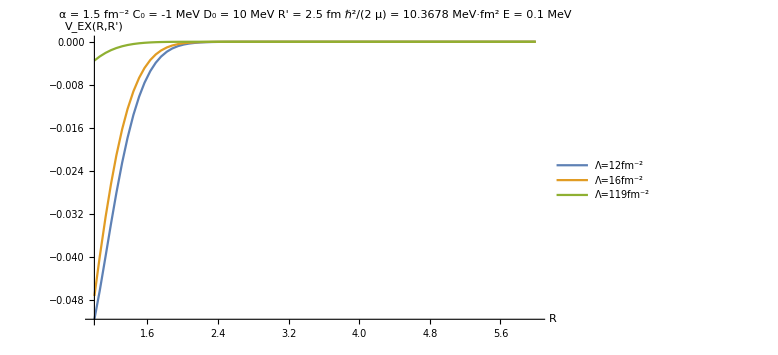
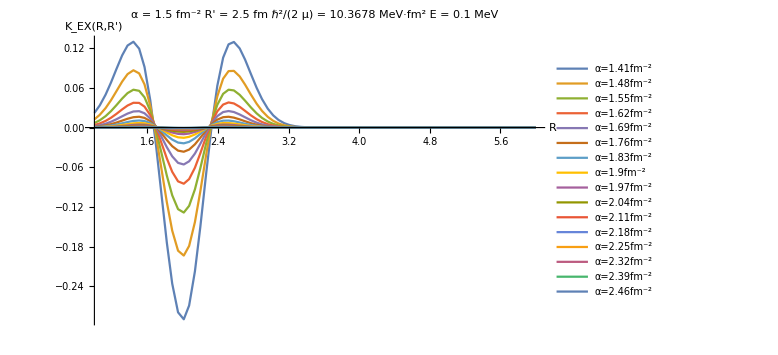
-Graphics- | -Graphics-

```mathematica
ℏc=197.32858;Mnucl=(938.2796+939.5731)/2.;
mu=Mnucl Z[[1]] Z[[2]]/(Z[[1]]+Z[[2]]);
hbc2m=ℏc^2/(2 mu);

Rmax=6.0;y0=2.5;alpha=1.5;c0=-1;d0=10;en=0.10;lambdas={12,16,119};alphas=Table[0.01+n 0.07,{n,20,35}];

Grid[{{
Plot[Evaluate@Table[ExchangePotential[r,y0,alpha,lambda,c0,d0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","V_EX(R,R')"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large,PlotLabel->"α = "<>ToString[alpha]<>" fm^-2   C_0 = "<>ToString[c0]<>" MeV    D_0 = "<>ToString[d0]<>" MeV    R' = "<>ToString[y0]<>" fm    ℏ^2/(2  μ) = "<>ToString[hbc2m]<>" MeV·fm^2     E = "<>ToString[en]<>" MeV"],
Plot[Evaluate@Table[ExchangeKernel[r,y0,alpha,en,hbc2m],{alpha,alphas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","K_EX(R,R')"},PlotLegends->Table["α="<>ToString[n]<>"fm^-2",{n,alphas}],PlotRange->Full,ImageSize->Large,PlotLabel->"α = "<>ToString[alpha]<>" fm^-2    R' = "<>ToString[y0]<>" fm    ℏ^2/(2  μ) = "<>ToString[hbc2m]<>" MeV·fm^2     E = "<>ToString[en]<>" MeV"]
}}]
```

```mathematica
bet=3;gam=1;
exponent=Function[{r,rp,alpha,beta,gamma},Exp[-alpha r^2-gamma rp^2] Cosh[beta r rp]];
Animate[Plot3D[exponent[r,rp,alf,bet,gam],{r,-3,3},{rp,-3,3},PlotRange->Full],{alf,1.1,10,0.1},AnimationRunning->False]
```

```mathematica
ThreeJSymbol[{1,0},{0,0},{1,0}]
SphericalBesselJ[3,0]
```

-1/(√3)

0

```mathematica
Clear[a,lam,c,d,e]
terme=Table[1/(2 normierung) RGMequationComponents[[m]]/.{x->r,y->rp,α->a,Λ->lam,"C_0"->c,"D_1"->d,"E"->e,"-ℏ^2/(2  μ)·"->hbc2m},{m,1,Length[RGMequationComponents]-16}];
termekin=Table[1/(2 normierung) RGMequationComponents[[m]]/.{x->r,y->rp,α->a,Λ->lam,"C_0"->c,"D_1"->d,"E"->e,"-ℏ^2/(2  μ)·"->hbc2m},{m,Length[RGMequationComponents]-16+1,Length[RGMequationComponents]}];
```

```mathematica
Simplify[Total[termekin]]
```

(T̂-E)+1/9 (T̂-E) a^(3/2) (432 √2 ⅇ^(-2 a (r^2+rp^2))-256 √6 ⅇ^(-2/3 a (5 r^2-8 r rp+5 rp^2))-256 √6 ⅇ^(-2/3 a (5 r^2+8 r rp+5 rp^2)))

```mathematica
termeLargeL=Table[Normal[Series[Coefficient[terme[[mm]]/.Exponent[terme[[mm]],E]->n,E^n],{a,0,5}]] Exp[Limit[Exponent[terme[[mm]],E],lam->Infinity]],{mm,1,Length[terme]}];
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

```mathematica
Total[termeLargeL]
```

24 ⅇ^(-2 a r^2) ((639 a^5 d)/(16 √2 lam^5)-(21 a^4 d)/(2 √2 lam^4)+(√2 a^3 d)/lam^3)+24 ⅇ^(-2 a r^2) ((111 a^5 d)/(4 √2 lam^5)-(9 a^4 d)/(√2 lam^4)+(√2 a^3 d)/lam^3)+24 ⅇ^(-(4 a r^2)/3) (-(560 a^(9/2) c)/(81 √3 lam^(9/2))+(40 a^(7/2) c)/(9 √3 lam^(7/2))-(8 a^(5/2) c)/(3 √3 lam^(5/2))+(4 a^(3/2) c)/(3 √3 lam^(3/2)))+24 ⅇ^(-4 a (r^2-r rp+rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-4 a (r^2+r rp+rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-2 a (3 r^2-4 r rp+2 rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-2 a (3 r^2+4 r rp+2 rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+12 ⅇ^(-4 a (r^2-r rp+rp^2)) ((240 a^5 c)/lam^(7/2)-(96 a^4 c)/lam^(5/2)+(32 a^3 c)/lam^(3/2))+12 ⅇ^(-4 a (r^2+r rp+rp^2)) ((240 a^5 c)/lam^(7/2)-(96 a^4 c)/lam^(5/2)+(32 a^3 c)/lam^(3/2))+48 ⅇ^(-2/3 a (5 r^2+3 rp^2)) ((640 √(2/3) a^5 c)/(9 lam^(7/2))-(128 √(2/3) a^4 c)/(3 lam^(5/2))+(64 √(2/3) a^3 c)/(3 lam^(3/2)))+(1536 a^(9/2) d ⅇ^(-2 a (2 r^2+rp^2)))/lam^3-(3072 √2 a^(9/2) d ⅇ^(-2 a (3 r^2-4 r rp+3 rp^2)))/lam^3-(3072 √2 a^(9/2) d ⅇ^(-2 a (3 r^2+4 r rp+3 rp^2)))/lam^3-(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (19 r^2-24 r rp+11 rp^2)))/(5 lam^3)+(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (11 r^2-8 r rp+11 rp^2)))/(5 lam^3)+(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (11 r^2+8 r rp+11 rp^2)))/(5 lam^3)-(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (19 r^2+24 r rp+11 rp^2)))/(5 lam^3)

```mathematica
Simplify[%]
```

12/25 ((3200 a^(9/2) d ⅇ^(-2 a (2 r^2+rp^2)))/lam^3-(6400 √2 a^(9/2) d ⅇ^(-2 a (3 r^2-4 r rp+3 rp^2)))/lam^3-(6400 √2 a^(9/2) d ⅇ^(-2 a (3 r^2+4 r rp+3 rp^2)))/lam^3-(1024 √10 a^(9/2) d ⅇ^(-2/5 a (19 r^2-24 r rp+11 rp^2)))/lam^3+(1024 √10 a^(9/2) d ⅇ^(-2/5 a (11 r^2-8 r rp+11 rp^2)))/lam^3+(1024 √10 a^(9/2) d ⅇ^(-2/5 a (11 r^2+8 r rp+11 rp^2)))/lam^3-(1024 √10 a^(9/2) d ⅇ^(-2/5 a (19 r^2+24 r rp+11 rp^2)))/lam^3+(400 a^3 c ⅇ^(-4 a (r^2-r rp+rp^2)) (15 a^2-6 a lam+2 lam^2))/lam^(7/2)+(400 a^3 c ⅇ^(-4 a (r^2+r rp+rp^2)) (15 a^2-6 a lam+2 lam^2))/lam^(7/2)+(6400 √(2/3) a^3 c ⅇ^(-2/3 a (5 r^2+3 rp^2)) (10 a^2-6 a lam+3 lam^2))/(9 lam^(7/2))+(25 a^3 d ⅇ^(-2 a r^2) (111 a^2-36 a lam+8 lam^2))/(2 √2 lam^5)+(25 a^3 d ⅇ^(-2 a r^2) (639 a^2-168 a lam+32 lam^2))/(8 √2 lam^5)-(50 a^3 c ⅇ^(-4 a (r^2-r rp+rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-4 a (r^2+r rp+rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-2 a (3 r^2-4 r rp+2 rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-2 a (3 r^2+4 r rp+2 rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)+(200 a^(3/2) c ⅇ^(-(4 a r^2)/3) (-140 a^3+90 a^2 lam-54 a lam^2+27 lam^3))/(81 √3 lam^(9/2)))